```mathematica
ClearAll["Global`*"];
```

#### -Graphics-

```mathematica
MassUnit = 1.445*10^-25*Quantity["Kilograms"]; (*Choose this unit so that Rb87=1[M]*)
TimeUnit=0.1/(2π)*Quantity["Seconds"];(*Then choose time unit by 0.1/2pi s*)
LengthUnit=Sqrt[(Quantity["ReducedPlanckConstant"]*TimeUnit)/MassUnit];(*Then we can calculate length unit*)
```

```mathematica
MassUnit
TimeUnit
UnitConvert[LengthUnit,"Meters"]
```

1.445×10^-25 kg

0.0159155 s

3.40811×10^-6 m

#### Define parameters and constants

```mathematica
ℏ=Quantity["ReducedPlanckConstant"]/(LengthUnit^2*MassUnit/TimeUnit)
omg=2π*Quantity[70,"Hertz"]*TimeUnit (*Harmonic trap frequency*)
m=1
```

1.

7.

1

```mathematica
l=Sqrt[ℏ/(m*omg)](*Harmonic length, which tells us the scale of trapped system*)
```

0.377964

```mathematica
xl=5(*Length for simulation in [L]*)
Nx=40 (*Number of grid points larger than 0*)
dx=xl/(Nx+1);
xgrid=Range[Nx]*dx (*Here we only consider the positive side of x axis since it is spherically symmetric*)
```

5

40

{5/41,10/41,15/41,20/41,25/41,30/41,35/41,40/41,45/41,50/41,55/41,60/41,65/41,70/41,75/41,80/41,85/41,90/41,95/41,100/41,105/41,110/41,115/41,120/41,125/41,130/41,135/41,140/41,145/41,150/41,155/41,160/41,165/41,170/41,175/41,180/41,185/41,190/41,195/41,200/41}

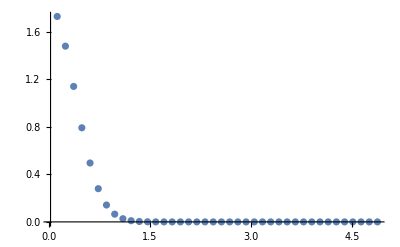

```mathematica
ana[r_]:=((m omg)/(π ℏ))^(3/4)Exp[-m omg r^2/(2ℏ)] (*Analytical solution*)
ListPlot[Transpose[{xgrid,ana[xgrid]}],PlotRange->All]
```

#### Some other scales -Graphics-